```mathematica
FourierTransform[Sin[t],t,ω]
```

ⅈ √(π/2) DiracDelta[-1+ω]-ⅈ √(π/2) DiracDelta[1+ω]

```mathematica
FourierTransform[Exp[-t^2],t,ω]
```

(ⅇ^(-ω^2/4))/(√2)

```mathematica
Denominator[(ⅇ^(-ω^2/4))/(√2)]
```

√2 ⅇ^(ω^2/4)

```mathematica
(*Definir las constantes*)τs=0.03*10^-12;  (*en segundos*)
τc=0.5*10^-12;   (*en segundos*)
τp=0.048*10^-12; (*en segundos*)
μe=1;            (*valor genérico para la movilidad electrónica*)
EDC=1;           (*campo eléctrico D*)
I0opt=1;         (*intensidad de la luz*)

(*Definir la función I_PC(t)*)
IPC[t_]:=(Sqrt[Pi]/2)*μe*EDC*I0opt*(Exp[(τp^2/(4*τc^2))-t/τc]*Erfc[(τp/(2*τc))-(t/τp)]-Exp[(τp^2/(4*τs^2))-t/τs]*Erfc[(τp/(2*τs))-(t/τp)])
```

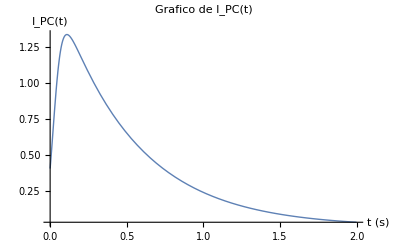

```mathematica
Plot[IPC[t],{t,0,2*10^-12},PlotRange->All,AxesLabel->{"t (s)","I_PC(t)"},PlotLabel->"Grafico de I_PC(t)",PlotStyle->Thick]
```

```mathematica
(*Derivar la función respecto al tiempo t*)dIPCdt=D[(Sqrt[Pi]/2)*μe*EDC*I0opt*(Exp[(τp^2/(4*τc^2))-t/τc]*Erfc[(τp/(2*τc))-(t/τp)]-Exp[(τp^2/(4*τs^2))-t/τs]*Erfc[(τp/(2*τs))-(t/τp)]),t]
```

1/2 √π (-2.35079×10^13 ⅇ^(0.64-(0.8-2.08333×10^13 t)^2-3.33333×10^13 t)+2.35079×10^13 ⅇ^(0.002304-(0.048-2.08333×10^13 t)^2-2.×10^12 t)-2.×10^12 ⅇ^(0.002304-2.×10^12 t) Erfc[0.048-2.08333×10^13 t]+3.33333×10^13 ⅇ^(0.64-3.33333×10^13 t) Erfc[0.8-2.08333×10^13 t])

```mathematica
(*Simplificar la expresión derivada*)Simplify[dIPCdt]
```

-1.77654×10^12 ⅇ^(-2.×10^12 t) Erfc[0.048-2.08333×10^13 t]+5.60237×10^13 ⅇ^(-3.33333×10^13 t) Erfc[0.8-2.08333×10^13 t]

```mathematica
(*Graficar la derivada de I_PC(t)*){{□}, {Plot[dIPCdt,{t,-2*10^-12,2*10^-12},PlotRange->All,AxesLabel->{"t (s)","dI_PC/dt"},PlotLabel->"Derivada de I_PC(t)",PlotStyle->Thick]}, {□}, {□}}
```

General::munfl: Exp[-1735.97] is too small to represent as a normalized machine number; precision may be lost.

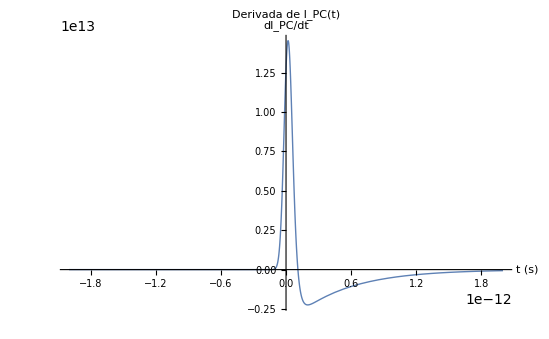
```mathematica
{{□},{-Graphics-},{□},{□}}
```

```mathematica
(*Define the variables using valid names*)muE=Symbol["muE"];
EDC=Symbol["EDC"]; (*Remove underscores*)
Iopt0=Symbol["Iopt0"];
tauP=Symbol["tauP"]; (*Rename tau_p to tauP*)
tauC=Symbol["tauC"]; (*Rename tau_c to tauC*)
tauCS=Symbol["tauCS"]; (*Rename tau_cs to tauCS*)

(*Define the function IPC(t) based on the given expression*)
IPC[t_]:=Sqrt[Pi]/2*muE*EDC*Iopt0*(Exp[(tauP^2/(4*tauC^2))-t/tauC]*Erfc[tauP/(2*tauC)-t/tauP]-Exp[(tauP^2/(4*tauCS^2))-t/tauCS]*Erfc[tauP/(2*tauCS)-t/tauP])

(*Compute the time derivative of IPC(t)*)
derivativeIPC=D[IPC[t],t]

(*Simplify the result*)
Simplify[derivativeIPC]
```

1/2 muE √π ((2 ⅇ^(-t/tauC+tauP^2/(4 tauC^2)-(-t/tauP+tauP/(2 tauC))^2))/(√π tauP)-(2 ⅇ^(-t/tauCS+tauP^2/(4 tauCS^2)-(-t/tauP+tauP/(2 tauCS))^2))/(√π tauP)-(ⅇ^(-t/tauC+tauP^2/(4 tauC^2)) Erfc[-t/tauP+tauP/(2 tauC)])/tauC+(ⅇ^(-t/tauCS+tauP^2/(4 tauCS^2)) Erfc[-t/tauP+tauP/(2 tauCS)])/tauCS) Symbol[E_DC] Symbol[I_opt^0]

(ⅇ^(-t (1/tauC+1/tauCS)) muE √π (-ⅇ^(t/tauCS+tauP^2/(4 tauC^2)) tauCS Erfc[-t/tauP+tauP/(2 tauC)]+ⅇ^(t/tauC+tauP^2/(4 tauCS^2)) tauC Erfc[-t/tauP+tauP/(2 tauCS)]) Symbol[E_DC] Symbol[I_opt^0])/(2 tauC tauCS)

```mathematica
FourierTransform[Simplify[derivativeIPC],t,ω]
```

```mathematica
(*Calcular la transformada de Fourier de Erfc[x]*)
```

{{(-(ⅈ ⅇ^(-ω^2/4) √(2/π))/ω+√(2 π) DiracDelta[ω])^2},{□}}

```mathematica
(*Calcular la transformada de Fourier de Erfc[x]*)fourierErfc=FourierTransform[Erfc[x],x,ω]

(*Simplificar el resultado*)
Simplify[fourierErfc]
```

-(ⅈ ⅇ^(-ω^2/4) √(2/π))/ω+√(2 π) DiracDelta[ω]

-(ⅈ ⅇ^(-ω^2/4) √(2/π))/ω+√(2 π) DiracDelta[ω]

```mathematica
(*Definimos las variables y los parámetros que aparecen en la ecuación*)alpha=Symbol["α"];
tauC=Symbol["τc"];
tauCS=Symbol["τcs"];
tauP=Symbol["τp"];
t=Symbol["t"];
omega=Symbol["ω"];

(*Definimos la función en el dominio del tiempo*)
ETHz[t_]:=alpha*Exp[-t*(tauC+tauCS)/(tauC*tauCS)]*(tauC*Erf[-t/tauP+tauP/(2*tauCS)]*Exp[t/tauC+tauP^2/(4*tauCS^2)]-tauCS*Erf[-t/tauP]*Exp[t/tauCS+tauP^2/(4*tauC^2)]);

(*Calculamos la transformada de Fourier*)
fourierTransform=FourierTransform[ETHz[t],t,omega]

(*Mostramos el resultado*)
Simplify[fourierTransform]
```

$Aborted

fourierTransform

```mathematica
fourierErfcExp=FourierTransform[Erfc[x]Exp[a*x],x,ω]

(*Simplificar el resultado*)
Simplify[fourierErfcExp]
```

(ⅇ^(1/4 (a+ⅈ ω)^2) √(2/π))/(a+ⅈ ω)

(ⅇ^(1/4 (a+ⅈ ω)^2) √(2/π))/(a+ⅈ ω)

```mathematica
Simplify[fourierErfcExp]
```

```mathematica
Simplify[FourierTransform[Exp[-x],x,ω]]
```

FourierTransform[ⅇ^-x,x,ω]

```mathematica
fourierErfcExp=FourierTransform[Exp[-1/4*a^2*x^2]*(i),x,ω]
```

```mathematica
(*Definimos la función en el dominio de la frecuencia,extraída de la imagen*)
FETH[omega_]:=alpha*tauC*tauCS*Sqrt[2/Pi]*Exp[-(1/4)*tauC^2*omega^2]*(I*omega*tauCS-I*omega*tauC);

(*Definimos la transformada de Fourier de la función rectángulo*)
rectangularFT[omega_]:=Sinc[omega]
```

```mathematica
(*Calcular la convolución de f(t) y g(t)*)
convolucion=Convolve[FETH[x],rectangularFT[x],x,t]

(*Mostrar el resultado*)
Simplify[convolucion]
```

√(2/π) α τc τcs Convolve[ⅇ^(-1/4 x^2 τc^2) (-ⅈ x τc+ⅈ x τcs),Sinc[x],x,t]

-ⅈ √(2/π) α τc (τc-τcs) τcs Convolve[ⅇ^(-1/4 x^2 τc^2) x,Sinc[x],x,t]

```mathematica
convolucion
```

√(2/π) α τc τcs Convolve[ⅇ^(-1/4 x^2 τc^2) (-1/(1+ⅈ x τc)+1/(1+ⅈ x τcs)),ⅇ^(-x^2),x,t]